```mathematica
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(0.95*M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]
```

-((1. Bm ts (-1.+η))/(Em (Log[1.-1. 0.95^(1.-1. η) ((B0/Bm)^(1/(-1.+η)) M)^(1.-1. η)]-1. Log[1.-1. ((B0/Bm)^(1/(-1.+η)) M (1.-1. f0 M^(-1.+γ)))^(1.-1. η)])))

```mathematica
BMRecovery=Recovery/.{ts->1,B0->4.7*10^(-2),Em->5774(*J/gram*),η->3/4,η2->-0.206,λ0->3.3879*10^(-7),ef->0.001,γ->1.19,ζ->1.01,f0->0.0202,mm0->0.324}
```

(0.0000432975 Bm)/(Log[1.-21.0055 (M/(1/Bm)^4.)^0.25]-1. Log[1.-21.2766 (((1.-0.0202 M^0.19) M)/(1/Bm)^4.)^0.25])

```mathematica
BM2Recovery=BMRecovery/.{Bm->B0*M^(-1/4),η->3/4}
```

(0.0000432975 B0)/(M^(1/4) (Log[1.-21.0055 (M/((M^(1/4)/B0)^4.))^0.25]-1. Log[1.-21.2766 (((1.-0.0202 M^0.19) M)/((M^(1/4)/B0)^4.))^0.25]))

```mathematica
BM2Recovery/.B0->4.7*10^(-2)
```

(2.03498×10^-6)/(M^(1/4) (-4.36289-1. Log[1.-1. (1.-0.0202 M^0.19)^0.25]))

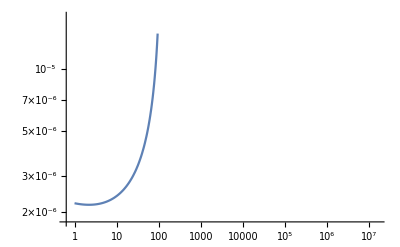

```mathematica
LogLogPlot[%,{M,1,10^7}]
```